# Optical Mode Matching

#### - Mode-matching to a cavity with known length, TEM00 mode waist, mirror radii of curvature: Mark’s notes 6.4. - Calculating a cavity mode waist: Mark’s notes 6.2

## General Misc. Functions

### Gaussian beam stuff (in vacuum)

```mathematica
Clear[zR,w,R,η,q]
zR[w0_]:=(π  w0^2)/λ;(*Rayleigh range in vacuum [m]*)
w[z_,w0_]:= w0(1+(z/zR[w0])^2)^(1/2);(*beam waist [m]*)
RoC[z_,w0_]:= z(1+zR[w0]^2/z^2);(*RoC [m]*)
η[z_,w0_]:=ArcTan[z/zR[w0]];(*Guoy phase*)
q[z_,w0_]:=1/(1/RoC[z,w0]+(ⅈ λ)/(π w[z,w0]^2)); (*the mysterious q parameter*)
qM[q_,M_]:=(M[[1,1]]q+M[[1,2]])/(M[[2,1]]q+M[[2,2]]); (*q after an ABCD matrix M is applied*)
wq[q_,z_]:=√(λ/(π Im[1/(q+z)]));
```

### ABCD Matrices

```mathematica
ThinLensM[f_]:={{1,0},{-1/f,1}};
FreeSpaceM[d_]:={{1,d},{0,1}};
CavMirrorM={{1,t/ng},{(-1+ng)/R,(ng+((-1+ng) t)/R)/ng}};
```

### Misc functions

```mathematica
(*This applies the transformations to the beam and plots the waist as a function of the optical axis*)
beamPropagate[qInit_,sys_]:=Module[{q=qInit,qNext,plots={},i,element,z=0,zNext,x},
For[i=1,i≤Length[sys],i++,
element=sys[[i]];
qNext=qM[q,element[[1]]];
zNext=z+element[[2]];
AppendTo[plots,Piecewise[{{wq[qNext,x-z]/10^-3,z<x<zNext}}]];
q=qNext+element[[2]];
z=zNext;
]; (*waist in [m]*)
Plot[plots,{x,0,z},PlotRange->{0,All},Frame->False]
]
```

## Linear Symmetric Cavity

Assumes radii of curvature for mirrors M1, M2 are R1=R2=R, and therefore g1=g2=g, and the waist forms halfway down the length L of the cavity.

```mathematica
Clear[z1,z2,plots]
```

Parameters for the Raman 6.8 GHz filter cavity

```mathematica
R= .500; (*[m]*)
L = .022; (*[m]*)
λ = 780*10^-9; (*[m]*)
ng = 1.45; (*mirror glass index of refraction*)
t = 6.35*10^-3; (*mirror thickness [m]; need to check this*)
g = 1 - L/R;
nn = 1 - ng; (*Mark's ñ*)
```

```mathematica
wCavMode[L_,R_]:= (λ/(2 π))^(1/2)(L(2 R -L))^(1/4); (*TEM00 cavity waist*)
wIntraCav[w0_,z0_]:=(w0 R)/(√(nn^2 zR[w0]^2+(R-nn (z0-nn/ng t))^2));(*waist of the beam inside the cavity if the beam focuses to w0 at z0 when M1 is removed*)
zIntraCav[z0_,w0_]:=R((R-nn (z0-nn/ng t))(z0-nn/ng t)-nn zR[w0]^2)/((R-nn (z0-nn/ng t))^2+nn^2 zR[w0]^2);(*location of beam focus inside the cavity wrt the nearest lens to left, if the beam focuses to w0 at z0 when M1 is removed*)
```

#### Cavity mode matching graphical validation

Mode f1,f2 lenses I have on hand. d1,d2 from filter_cav_modematch.nb adapted from B. Grinkmeyer’s code. Needs to be cleaned up and ported over here.

```mathematica
Clear[f1,f2,d1,d2]
```

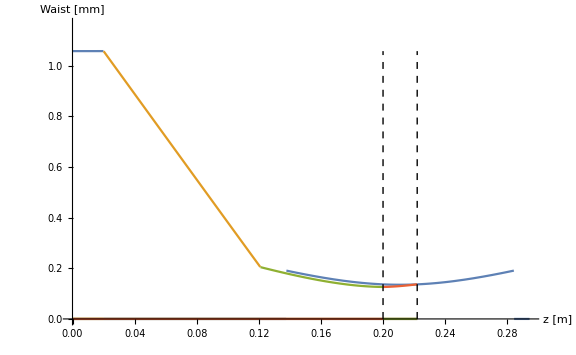

```mathematica
wCavity = wCavMode[L,R]; 
zRCav = zR[wCavity];
w0 = 0.001057;
q0 = Limit[q[b,w0],b->0];
f1 = .125; d1 = 0.101;
f2 = -.03; d2 =0.079; (*0.09125;*)
d0 = 0.02;
dCavity = d0+d1+d2+L/2; (*cavity center*)
lenses = {{FreeSpaceM[d0],d0},{ThinLensM[f1],d1},{ThinLensM[f2],d2},{CavMirrorM,L}};
Show[Plot[Piecewise[{{w[z-dCavity,wCavity]/10^-3,dCavity-zRCav<z <dCavity+zRCav}}],{z,0,dCavity+zRCav+0.01},PlotRange->{0,1.1w0/10^-3}],beamPropagate[q0,lenses],Graphics[{Dashed,Line[{{dCavity-L/2,0},{dCavity-L/2,w0/10^-3}}]}],Graphics[{Dashed,Line[{{dCavity+L/2,0},{dCavity+L/2,w0/10^-3}}]}],AxesLabel->{"z [m]","Waist [mm]"},ImageSize->Large]
```

Numerically solve for the correct cavity waist and position

```mathematica
wCavity
```

0.000134942

```mathematica
dCavity
```

0.22325

```mathematica
NSolve[wIntraCav[wo,zo]==wCavity && zIntraCav[wo,zo]==dCavity]
```

{{wo→-0.00203986,zo→-0.000371949},{wo→0.00203986,zo→-0.000370923},{wo→-0.00203985-3.02011×10^-9 ⅈ,zo→0.-0.000371949 ⅈ},{wo→-0.00203985+3.02011×10^-9 ⅈ,zo→0.+0.000371949 ⅈ},{wo→0.00203985-3.01179×10^-9 ⅈ,zo→0.+0.000370923 ⅈ},{wo→0.00203985+3.01179×10^-9 ⅈ,zo→0.-0.000370923 ⅈ},{wo→0.00203985,zo→0.000370923},{wo→-0.00203985,zo→0.000371949},{wo→-0.000135525,zo→0.000371472},{wo→0.000135525,zo→0.000371404},{wo→0.000135479+4.54059×10^-8 ⅈ,zo→0.+0.000371404 ⅈ},{wo→0.000135479-4.54059×10^-8 ⅈ,zo→0.-0.000371404 ⅈ},{wo→-0.000135479-4.54143×10^-8 ⅈ,zo→0.+0.000371472 ⅈ},{wo→-0.000135479+4.54143×10^-8 ⅈ,zo→0.-0.000371472 ⅈ},{wo→0.000135434,zo→-0.000371404},{wo→-0.000135434,zo→-0.000371472}}

Possible solutions

```mathematica
(*Clear[w0,R,nn,ng,t,z0]*)
```

```mathematica
(*Solve[w2Sq==(w0Sq R^2)/(nn^2 zR w0Sq+(R-nn (z0-nn/ng t))^2),w0Sq]*)(*w2 = the desired cavity waist, w0 the beam waist w/o M1 coupler installed*)
```

```mathematica
(*wFinal[w2_,z0_]:=(w2 (ng R+nn^2 t-ng nn z0))/(ng √(R^2-nn^2 w2^2 zR)); (*where cavity mode should form if coupled beam focuses to w0,z0*)*)
```

Get the final beam waist and location

```mathematica
beamWaistFinal[qInit_,sys_]:=Module[{q=qInit,qNext,i,element,z=0,zNext,x},
For[i=1,i≤Length[sys],i++,
element=sys[[i]];
qNext=qM[q,element[[1]]];
zNext=z+element[[2]];
Print[FindMinimum[{wq[qNext,x-z]/10^-3,z<x<zNext},{x,z}]]
Print[]
q=qNext+element[[2]];
z=zNext;
](*waist in [m]*)
]
```

```mathematica
beamWaistFinal[q0,lenses]
```

{1.00001,{x$71444→0.000117175}}

Set::write: Tag Times in (0.-4.02768 ⅈ) Null Null is Protected.

{0.193631,{x$71444→0.121}}

Set::write: Tag Times in (0.-4.02768 ⅈ) Null Null is Protected.

{1.,{x$71444→0.121}}

Set::write: Tag Times in (0.-4.02768 ⅈ) Null Null is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

{1.,{x$71444→0.21225}}

```mathematica
beamWaistFinal2[qInit_,sys_]:=Module[{q=qInit,qNext,i,element,z=0,zNext,x},
For[i=1,i≤Length[sys],i++,
element=sys[[i]];
qNext=qM[q,element[[1]]];
zNext=z+element[[2]];
Print["q=",qNext,",z=",z,",zNext="zNext]
q=qNext+element[[2]];
z=zNext;
](*waist in [m]*)
]
```

```mathematica
Clear[f1,f2,d1,d2]
lenses = {{ThinLensM[f1],d1},{ThinLensM[f2],d2}};
beamWaistFinal2[q0,lenses]
```

q=-(0.+4.02768 ⅈ)/(1+(0.+4.02768 ⅈ)/f1),z=0,zNext= d1

Set::write: Tag Times in (0.-4.02768 ⅈ) Null is Protected.

q=-(0.+4.02768 ⅈ)/(1+(0.+4.02768 ⅈ)/f2),z=d1,zNext= (d1+d2)

Set::write: Tag Times in (0.-4.02768 ⅈ) Null is Protected.

```mathematica
Chop[{{1, 0},{(n-1)/r, n}}. {{1, th},{0, 1}}.{{1, 0},{0, 1/n}}]
```

{{1,th/n},{(-1+n)/r,(n+((-1+n) th)/r)/n}}